CASE OF SINGLE COLD PILL AND A COURSE OF PILLS
 Example :- Solve drug single cold pill model and plot its graph

{{x[t]→ⅇ^(-k1 t),y[t]→-(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1)/(k1-k2)}}

{ⅇ^(-1.386 t)}

{ⅇ^(-0.6931 t)}

{ⅇ^(-0.6931 t)}

{-1.11111 ⅇ^(-1.5246 t) (ⅇ^(0.1386 t)-ⅇ^(1.386 t))}

{-1.03448 ⅇ^(-0.7162 t) (ⅇ^(0.0231 t)-ⅇ^(0.6931 t))}

{-1.13048 ⅇ^(-0.7731 t) (ⅇ^(0.08 t)-ⅇ^(0.6931 t))}

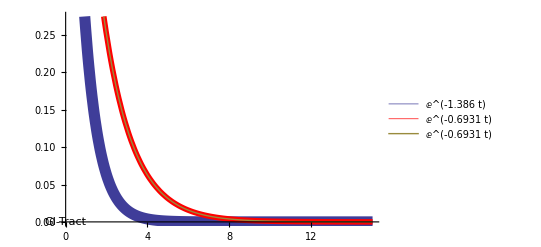

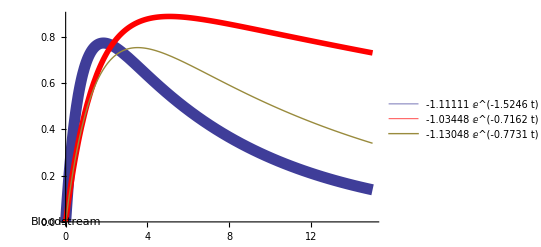

```mathematica
eqn1=x'[t]==-k1*x[t];
eqn2=y'[t]==k1*x[t]-k2*y[t];
sol=DSolve[{eqn1,eqn2,x[0]==1,y[0]==0},{x[t],y[t]},t]
solx1=x[t]/.sol/.{k1->1.3860,k2->0.1386}
solx2=x[t]/.sol/.{k1->0.6931,k2->0.0231}
solx3=x[t]/.sol/.{k1->0.6931,k2->0.08}
soly1=y[t]/.sol/.{k1->1.3860,k2->0.1386}
soly2=y[t]/.sol/.{k1->0.6931,k2->0.0231}
soly3=y[t]/.sol/.{k1->0.6931,k2->0.08}
Plot[{solx1,solx2,solx3},{t,0,15},PlotStyle->{Thickness[0.02],{Red,Thickness[0.01]},Thick},Epilog->Inset[Framed[GI-Tract]],PlotLegends->"Expressions"]
Plot[{soly1,soly2,soly3},{t,0,15},PlotStyle->{Thickness[0.02],{Red,Thickness[0.01]},Thick},Epilog->Inset[Framed[Bloodstream]],PlotLegends->"Expressions"]
```

Example :- Solve course of cold pills model and plot its graph

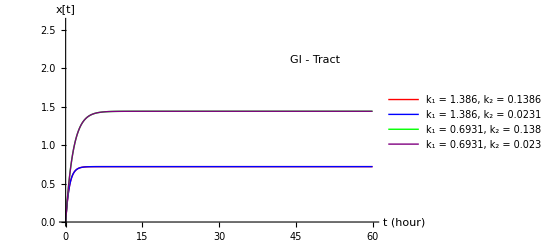

```mathematica
Clear[eqn1,eqn2,sol,k1vals,k2vals]

eqn1=x'[t]==I-k1*x[t];
eqn2=y'[t]==k1*x[t]-k2*y[t];

(*Solve symbolically*)
sol=DSolve[{eqn1,eqn2,x[0]==0,y[0]==0},{x[t],y[t]},t];

(*Choose multiple k1 and k2 values*)
k1vals={1.3860,0.6931};
k2vals={0.1386,0.0231};

(*Plot x[t] for each (k1,k2) pair*)
plots=Table[Evaluate[x[t]/.First[sol]/.{k1->k1val,k2->k2val,I->1}],{k1val,k1vals},{k2val,k2vals}];

(*Flatten plots (since it's a 2D table)*)
flatPlots=Flatten[plots];

(*Plot with legend and formatting*)
Plot[flatPlots,{t,0,60},PlotRange->{0,2.6},AxesLabel->{"t (hour)","x[t]"},AxesStyle->Arrowheads[{0,0.05}],PlotStyle->{Red,Blue,Green,Purple},PlotLegends->Placed[LineLegend[Automatic,Flatten[Table["k₁ = "<>ToString[k1val]<>", k₂ = "<>ToString[k2val],{k1val,k1vals},{k2val,k2vals}]]],Below],Epilog->Inset[Framed["GI - Tract"],Scaled[{0.8,0.8}]]]
```